```mathematica
(* SIR (Eimeria) PREVALENCE *)
```

```mathematica
(* Turn off Solve warning messages *)
Off[Solve::ratnz]

(* Function to generate table of mean burdens for ρ=0 and ρ=1, for all θ1 and θ2 combinations *)
provchange[pars_]:=
Module[{data},
data= Table[Table[Solve[system//.provpars//.pars,{prev,eggs,n}][[3]],{prov,0,1}],{θ1,0,5},{θ2,0,5}];
Table[(prev/.data[[i]][[j]][[2]])-(prev/.data[[i]][[j]][[1]]),{i,1,6},{j,1,6}]
]

(* Provisioning response calculations *)
provpars={δp->δmin+(δmax-δmin)*E^(-θ1*prov),αp->αmax-(αmax-αmin)*E^(-θ2*prov)};

(* System equations *)
system={(1-prev)*(αp*δp*eggs- ν*prev)-prev*(b*(K-n)/K+γ)==0 && τ*prev*n-ϕ*eggs==0 && b*n*(K-n)/K-μ*n-ν*prev*n==0};
```

```mathematica
(* GENERATE PLOTS VARYING BY K *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};
pars2={K->42.12*1.5,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};
pars3={K->42.12*2,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.293317,0.351186,0.369002,0.37517,0.377389},{-0.242661,0.0788852,0.163496,0.189545,0.198563,0.201808},{-0.242661,-0.0600785,0.0418624,0.0732475,0.0841117,0.0880221},{-0.242661,-0.126691,-0.0164425,0.0175003,0.0292497,0.0334788},{-0.242661,-0.154012,-0.0403565,-0.00536473,0.00674788,0.0111076},{-0.242661,-0.164493,-0.0495302,-0.014136,-0.00188407,0.00252581}}

{{0.,0.195545,0.234124,0.246002,0.250113,0.251593},{-0.233319,0.0525901,0.108997,0.126364,0.132375,0.134539},{-0.384523,-0.0400523,0.0279083,0.0488317,0.0560745,0.0586814},{-0.457003,-0.0844604,-0.0109617,0.0116668,0.0194998,0.0223192},{-0.48673,-0.102675,-0.0269043,-0.00357649,0.00449859,0.00740508},{-0.495108,-0.109662,-0.0330201,-0.00942398,-0.00125605,0.00168387}}

{{0.,0.146659,0.175593,0.184501,0.187585,0.188695},{-0.17499,0.0394426,0.0817479,0.0947727,0.0992813,0.100904},{-0.288392,-0.0300393,0.0209312,0.0366238,0.0420558,0.044011},{-0.342752,-0.0633453,-0.00822125,0.00875013,0.0146249,0.0167394},{-0.365048,-0.077006,-0.0201783,-0.00268237,0.00337394,0.00555381},{-0.373601,-0.0822463,-0.0247651,-0.00706799,-0.000942035,0.00126291}}

-0.5

0.4

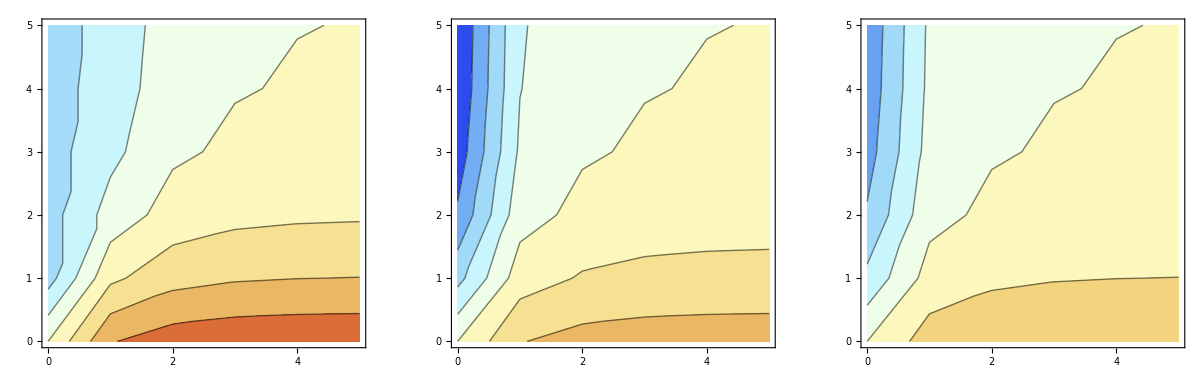

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY b *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};
pars2={K->42.12,b->1.24*1.5,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};
pars3={K->42.12,b->1.24*2,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.293317,0.351186,0.369002,0.37517,0.377389},{-0.242661,0.0788852,0.163496,0.189545,0.198563,0.201808},{-0.242661,-0.0600785,0.0418624,0.0732475,0.0841117,0.0880221},{-0.242661,-0.126691,-0.0164425,0.0175003,0.0292497,0.0334788},{-0.242661,-0.154012,-0.0403565,-0.00536473,0.00674788,0.0111076},{-0.242661,-0.164493,-0.0495302,-0.014136,-0.00188407,0.00252581}}

{{0.,0.28735,0.344041,0.361495,0.367536,0.369711},{-0.25807,0.0772802,0.160169,0.185689,0.194523,0.197702},{-0.25807,-0.0588562,0.0410107,0.0717573,0.0824004,0.0862312},{-0.25807,-0.124113,-0.016108,0.0171442,0.0286546,0.0327976},{-0.25807,-0.150878,-0.0395354,-0.00525558,0.00661059,0.0108816},{-0.25807,-0.161146,-0.0485224,-0.0138484,-0.00184574,0.00247442}}

{{0.,0.284456,0.340576,0.357854,0.363835,0.365988},{-0.265542,0.076502,0.158556,0.183819,0.192564,0.195711},{-0.265542,-0.0582634,0.0405977,0.0710346,0.0815706,0.0853628},{-0.265542,-0.122863,-0.0159457,0.0169715,0.0283661,0.0324673},{-0.265542,-0.149359,-0.0391373,-0.00520265,0.00654401,0.010772},{-0.265542,-0.159523,-0.0480338,-0.0137089,-0.00182715,0.0024495}}

-0.3

0.4

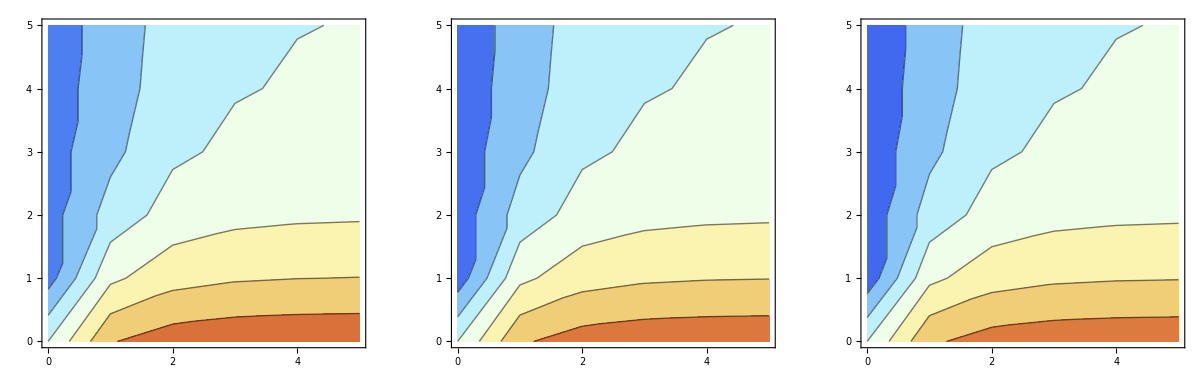

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY μ *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75,τ->717,ϕ->1/9};
pars2={K->42.12,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75/1.5,τ->717,ϕ->1/9};
pars3={K->42.12,b->1.24,δ->1,α->7.456*^-7,γ->0.1131,ν->0,δmin->δmax/2,δmax->9.59*^-2,αmin->1*^-5,αmax->2*^-5,μ ->1/13.75/2,τ->717,ϕ->1/9};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.293317,0.351186,0.369002,0.37517,0.377389},{-0.242661,0.0788852,0.163496,0.189545,0.198563,0.201808},{-0.242661,-0.0600785,0.0418624,0.0732475,0.0841117,0.0880221},{-0.242661,-0.126691,-0.0164425,0.0175003,0.0292497,0.0334788},{-0.242661,-0.154012,-0.0403565,-0.00536473,0.00674788,0.0111076},{-0.242661,-0.164493,-0.0495302,-0.014136,-0.00188407,0.00252581}}

{{0.,0.249863,0.299158,0.314335,0.319589,0.32148},{-0.29813,0.0671985,0.139274,0.161465,0.169146,0.171911},{-0.35486,-0.051178,0.0356605,0.062396,0.0716507,0.0749818},{-0.35486,-0.107922,-0.0140066,0.0149076,0.0249164,0.028519},{-0.35486,-0.131195,-0.0343778,-0.00456995,0.00574819,0.00946204},{-0.35486,-0.140123,-0.0421923,-0.0120418,-0.00160495,0.00215162}}

{{0.,0.228792,0.27393,0.287827,0.292638,0.294369},{-0.272989,0.0615317,0.127529,0.147848,0.154882,0.157413},{-0.409264,-0.0468622,0.0326533,0.0571342,0.0656084,0.0686586},{-0.409264,-0.0988207,-0.0128254,0.0136505,0.0228152,0.026114},{-0.409264,-0.120132,-0.0314787,-0.00418457,0.00526345,0.00866411},{-0.409264,-0.128307,-0.0386343,-0.0110263,-0.0014696,0.00197017}}

-0.5

0.4

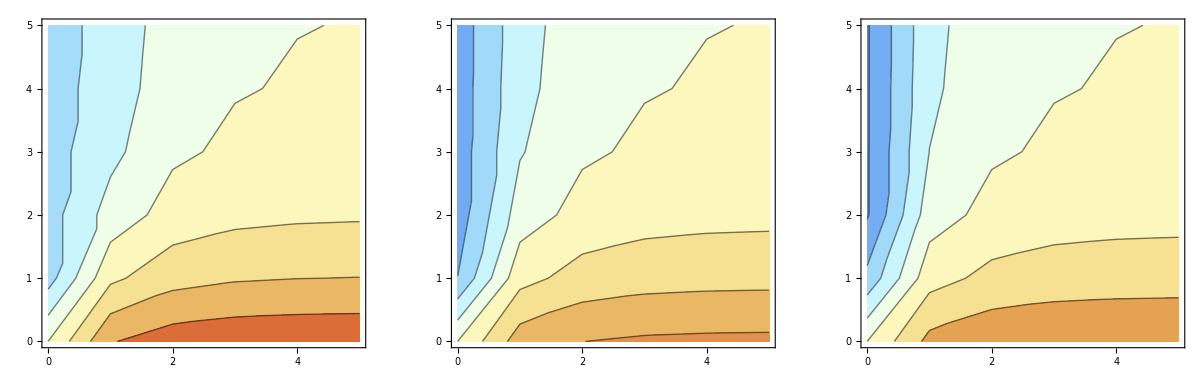

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```